```mathematica
x
```

x

```mathematica
ImportDataset["TRAIN5to50_40_10000_randomnew.mx"]
```

```mathematica
Clear[x,lengths]
```

```mathematica
lengths =x;
```

x

```mathematica
lengths
```

{k[k][k][k[s]]→3,18429,s[s[s[k][s]]][s[s[s]][s[s[s]]][k[s]][k[k][k[s]]][k[s][k][s[s[k[k]][s][s[s][s][s]]]][k[s][s[s[k[s[s][k[k[k]]]]]][k[s[k]][k[s[s]][1[k[s]]]]]]]]]→13}
 |  |  |  |

```mathematica
!(13===False)
```

True

```mathematica
DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_40_15000_randomnew_varlengths.mx",lengths];
```

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,!(#[[2]]=== False)&];
Length[NoHalt]
Length[Halt]
```

728

17703

```mathematica
HaltTrain = RandomSample[Halt,Length[NoHalt]];
```

```mathematica
HaltTrain[[1]]
```

s[k[s[k[s[k[k[s]]]]][k[s[k[s]][s[s]]]][s[k][s[k]][k]][k[s[s]][k]]]]→True

```mathematica
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
```

```mathematica
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
```

```mathematica
RasterTest = Join[HaltTrainRaster,NoHaltTrainRaster];
```

```mathematica
HaltTrainRaster
```

{-Graphics-→3,-Graphics-→10,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→7,-Graphics-→5,-Graphics-→7,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→5,-Graphics-→17,-Graphics-→3,-Graphics-→6,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→10,-Graphics-→14,-Graphics-→6,-Graphics-→18,-Graphics-→8,-Graphics-→3,-Graphics-→9,-Graphics-→3,-Graphics-→9,-Graphics-→7,-Graphics-→10,-Graphics-→14,-Graphics-→9,-Graphics-→8,-Graphics-→17,-Graphics-→14,-Graphics-→8,-Graphics-→7,-Graphics-→5,-Graphics-→10,-Graphics-→6,-Graphics-→7,-Graphics-→27,-Graphics-→2,-Graphics-→5,-Graphics-→8,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→9,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→7,-Graphics-→4,-Graphics-→5,-Graphics-→7,-Graphics-→5,-Graphics-→7,-Graphics-→3,-Graphics-→9,-Graphics-→25,-Graphics-→6,-Graphics-→7,-Graphics-→5,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→10,-Graphics-→3,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→11,-Graphics-→8,-Graphics-→3,-Graphics-→4,-Graphics-→9,-Graphics-→5,-Graphics-→12,-Graphics-→3,-Graphics-→16,-Graphics-→8,-Graphics-→3,-Graphics-→7,-Graphics-→4,-Graphics-→8,-Graphics-→6,-Graphics-→9,-Graphics-→4,-Graphics-→6,-Graphics-→7,-Graphics-→10,-Graphics-→5,-Graphics-→7,-Graphics-→10,-Graphics-→5,-Graphics-→4,-Graphics-→9,-Graphics-→2,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→16,-Graphics-→3,-Graphics-→7,-Graphics-→3,-Graphics-→5,-Graphics-→4,-Graphics-→8,-Graphics-→6,-Graphics-→3,-Graphics-→3,-Graphics-→6,-Graphics-→10,-Graphics-→6,-Graphics-→8,-Graphics-→8,-Graphics-→4,-Graphics-→7,-Graphics-→6,-Graphics-→3,-Graphics-→3,-Graphics-→5,-Graphics-→8,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→8,-Graphics-→3,-Graphics-→12,-Graphics-→3,-Graphics-→12,-Graphics-→3,-Graphics-→5,-Graphics-→4,-Graphics-→17,-Graphics-→7,-Graphics-→6,-Graphics-→3,-Graphics-→6,-Graphics-→4,-Graphics-→3,-Graphics-→8,-Graphics-→12,-Graphics-→3,-Graphics-→8,-Graphics-→4,-Graphics-→6,-Graphics-→8,-Graphics-→21,-Graphics-→4,-Graphics-→11,-Graphics-→9,-Graphics-→3,-Graphics-→14,-Graphics-→7,-Graphics-→11,-Graphics-→13,-Graphics-→11,-Graphics-→15,-Graphics-→8,-Graphics-→9,-Graphics-→6,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→8,-Graphics-→8,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→4,-Graphics-→8,-Graphics-→8,-Graphics-→13,-Graphics-→9,-Graphics-→4,-Graphics-→5,-Graphics-→15,-Graphics-→8,-Graphics-→6,-Graphics-→11,-Graphics-→3,-Graphics-→9,-Graphics-→14,-Graphics-→7,-Graphics-→7,-Graphics-→12,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→3,-Graphics-→13,-Graphics-→14,-Graphics-→7,-Graphics-→5,-Graphics-→5,-Graphics-→8,-Graphics-→3,-Graphics-→6,-Graphics-→5,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→7,-Graphics-→7,-Graphics-→4,-Graphics-→11,-Graphics-→8,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→5,-Graphics-→8,-Graphics-→4,-Graphics-→5,-Graphics-→8,-Graphics-→6,-Graphics-→6,-Graphics-→9,-Graphics-→10,-Graphics-→5,-Graphics-→12,-Graphics-→11,-Graphics-→4,-Graphics-→3,-Graphics-→10,-Graphics-→9,-Graphics-→6,-Graphics-→4,-Graphics-→10,-Graphics-→3,-Graphics-→6,-Graphics-→11,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→7,-Graphics-→7,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→4,-Graphics-→11,-Graphics-→4,-Graphics-→6,-Graphics-→11,-Graphics-→6,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→8,-Graphics-→7,-Graphics-→11,-Graphics-→6,-Graphics-→3,-Graphics-→8,-Graphics-→10,-Graphics-→5,-Graphics-→10,-Graphics-→8,-Graphics-→3,-Graphics-→12,-Graphics-→9,-Graphics-→4,-Graphics-→8,-Graphics-→3,-Graphics-→7,-Graphics-→14,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→9,-Graphics-→9,-Graphics-→3,-Graphics-→8,-Graphics-→5,-Graphics-→3,-Graphics-→7,-Graphics-→4,-Graphics-→17,-Graphics-→3,-Graphics-→5,-Graphics-→11,-Graphics-→18,-Graphics-→4,-Graphics-→7,-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→12,-Graphics-→8,-Graphics-→5,-Graphics-→7,-Graphics-→12,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→9,-Graphics-→7,-Graphics-→9,-Graphics-→3,-Graphics-→10,-Graphics-→10,-Graphics-→14,-Graphics-→3,-Graphics-→5,-Graphics-→6,-Graphics-→9,-Graphics-→4,-Graphics-→5,-Graphics-→14,-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→7,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→10,-Graphics-→15,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→9,-Graphics-→7,-Graphics-→6,-Graphics-→10,-Graphics-→4,-Graphics-→4,-Graphics-→9,-Graphics-→3,-Graphics-→8,-Graphics-→12,-Graphics-→13,-Graphics-→17,-Graphics-→8,-Graphics-→6,-Graphics-→13,-Graphics-→8,-Graphics-→3,-Graphics-→4,-Graphics-→9,-Graphics-→7,-Graphics-→31,-Graphics-→4,-Graphics-→4,-Graphics-→8,-Graphics-→15,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→5,-Graphics-→9,-Graphics-→8,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→8,-Graphics-→5,-Graphics-→4,-Graphics-→3,-Graphics-→9,-Graphics-→8,-Graphics-→7,-Graphics-→4,-Graphics-→5,-Graphics-→7,-Graphics-→5,-Graphics-→5,-Graphics-→16,-Graphics-→6,-Graphics-→10,-Graphics-→6,-Graphics-→15,-Graphics-→8,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→14,-Graphics-→17,-Graphics-→5,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→15,-Graphics-→12,-Graphics-→13,-Graphics-→7,-Graphics-→11,-Graphics-→4,-Graphics-→7,-Graphics-→19,-Graphics-→6,-Graphics-→8,-Graphics-→10,-Graphics-→16,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→5,-Graphics-→6,-Graphics-→28,-Graphics-→3,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→12,-Graphics-→3,-Graphics-→3,-Graphics-→10,-Graphics-→12,-Graphics-→4,-Graphics-→4,-Graphics-→11,-Graphics-→4,-Graphics-→5,-Graphics-→7,-Graphics-→3,-Graphics-→6,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→5,-Graphics-→7,-Graphics-→17,-Graphics-→6,-Graphics-→6,-Graphics-→17,-Graphics-→5,-Graphics-→9,-Graphics-→6,-Graphics-→13,-Graphics-→13,-Graphics-→5,-Graphics-→8,-Graphics-→12,-Graphics-→8,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→8,-Graphics-→10,-Graphics-→7,-Graphics-→6,-Graphics-→14,-Graphics-→5,-Graphics-→6,-Graphics-→2,-Graphics-→10,-Graphics-→9,-Graphics-→12,-Graphics-→20,-Graphics-→3,-Graphics-→18,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→9,-Graphics-→4,-Graphics-→7,-Graphics-→6,-Graphics-→5,-Graphics-→23,-Graphics-→9,-Graphics-→10,-Graphics-→12,-Graphics-→10,-Graphics-→4,-Graphics-→7,-Graphics-→4,-Graphics-→6,-Graphics-→10,-Graphics-→7,-Graphics-→4,-Graphics-→11,-Graphics-→8,-Graphics-→9,-Graphics-→7,-Graphics-→8,-Graphics-→6,-Graphics-→28,-Graphics-→4,-Graphics-→2,-Graphics-→17,-Graphics-→8,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→13,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→3,-Graphics-→19,-Graphics-→12,-Graphics-→6,-Graphics-→8,-Graphics-→6,-Graphics-→6,-Graphics-→3,-Graphics-→10,-Graphics-→11,-Graphics-→14,-Graphics-→6,-Graphics-→14,-Graphics-→10,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→12,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→5,-Graphics-→9,-Graphics-→12,-Graphics-→9,-Graphics-→4,-Graphics-→10,-Graphics-→6,-Graphics-→10,-Graphics-→6,-Graphics-→3,-Graphics-→5,-Graphics-→13,-Graphics-→5,-Graphics-→5,-Graphics-→17,-Graphics-→5,-Graphics-→12,-Graphics-→4,-Graphics-→6,-Graphics-→13,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→9,-Graphics-→5,-Graphics-→15,-Graphics-→10,-Graphics-→7,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→4,-Graphics-→4,-Graphics-→12,-Graphics-→8,-Graphics-→11,-Graphics-→6,-Graphics-→14,-Graphics-→4,-Graphics-→3,-Graphics-→7,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→8,-Graphics-→22,-Graphics-→3,-Graphics-→6,-Graphics-→3,-Graphics-→10,-Graphics-→4,-Graphics-→15,-Graphics-→5,-Graphics-→8,-Graphics-→3,-Graphics-→14,-Graphics-→9,-Graphics-→4,-Graphics-→7,-Graphics-→8,-Graphics-→4,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→8,-Graphics-→4,-Graphics-→3,-Graphics-→11,-Graphics-→8,-Graphics-→9,-Graphics-→14,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→10,-Graphics-→6,-Graphics-→8,-Graphics-→7,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→8,-Graphics-→7,-Graphics-→14,-Graphics-→9,-Graphics-→5,-Graphics-→9,-Graphics-→4,-Graphics-→2,-Graphics-→6,-Graphics-→12,-Graphics-→3,-Graphics-→6,-Graphics-→5,-Graphics-→5,-Graphics-→9,-Graphics-→9,-Graphics-→7,-Graphics-→5,-Graphics-→4,-Graphics-→12,-Graphics-→7,-Graphics-→3,-Graphics-→5,-Graphics-→20,-Graphics-→7,-Graphics-→5,-Graphics-→2,-Graphics-→7,-Graphics-→5,-Graphics-→13,-Graphics-→5,-Graphics-→8,-Graphics-→7,-Graphics-→7,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→15,-Graphics-→4,-Graphics-→7,-Graphics-→6,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→8,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→7,-Graphics-→10,-Graphics-→5,-Graphics-→5,-Graphics-→15,-Graphics-→10,-Graphics-→4,-Graphics-→3,-Graphics-→12,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→8,-Graphics-→8,-Graphics-→14,-Graphics-→3,-Graphics-→5,-Graphics-→9,-Graphics-→7,-Graphics-→7,-Graphics-→8,-Graphics-→14,-Graphics-→16,-Graphics-→3,-Graphics-→9,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→8,-Graphics-→6,-Graphics-→9,-Graphics-→6,-Graphics-→30,-Graphics-→15,-Graphics-→5,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→9}

```mathematica
DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/5to50_40_10000_rastertrain.mx",RasterTrain];
```

```mathematica
RasterPredict=RasterTest/.(a_->b_)/;b===False:> (a->0);
```

```mathematica
RasterPredict
```

```mathematica
HaltTrainRaster
```

{SKRasterize[s[s[k[k[k]]]][k[k[s]][s[k[k[k]][k]][s][s[s[s[k]]]][s][s[s[s][s]]][k[s][k][s[s[s][k][k]]][k[k[s[k]]][k[k][k[k][k[k]]]][s[s][k[k]]]]]]],5]→3,726,SKRasterize[1]→9}
 |  |  |  |

```mathematica
DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/5to50_40_10000_rastertrain.mx",RasterPredict];
```

```mathematica
ImportDataset["5to50_40_10000_rastertest.mx"]
```

```mathematica
Global`
```

```mathematica
RasterPredictor=Predict[RasterPredict]
```

PredictorFunction[…]

```mathematica
RasterClassifyTest=RasterTest/.(a_->b_)/;!(b===False):> (a->True);
```

```mathematica
RasterClassify=Classify[RasterClassif]
```

```mathematica
ClassifierFunction[…]
```

```mathematica
Export["5to50_40_10000_raster_classify.wmlf",RasterClassify]
```

5to50_40_10000_raster_classify.wmlf

```mathematica
RasterClassify=Import["5to50_40_10000_raster_classify.wmlf"]
```

ClassifierFunction[…]

0.818 accuracy (RandomForest) ... but is it just classifying based on the lines given?
0.758 accuracy with 5 lines.

0.8 accuracy with 5 lines for new random model

```mathematica
RasterMeasurements=ClassifierMeasurements[RasterClassify,RasterTest]
```

ClassifierMeasurementsObject[…]

```mathematica
RasterMeasurements["Accuracy"]
```

0.45057

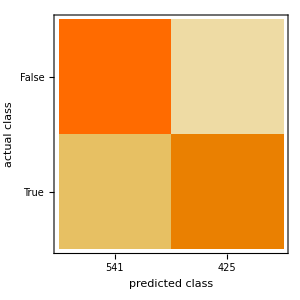

```mathematica
RasterMeasurements["ConfusionMatrixPlot"]
```

What about accuracy for other leaf sizes?

```mathematica
LeafSize40 = CreateTrainingData[x];
```

```mathematica
RasterMeasurements40 = ClassifierMeasurements[RasterClassify,LeafSize40]
```

ClassifierMeasurementsObject[…]

```mathematica
RasterMeasurements40["Accuracy"]
```

0.819444

```mathematica
LeafSize30 = CreateTrainingData[x];
```

```mathematica
RasterMeasurements30 = ClassifierMeasurements[RasterClassify,LeafSize40]
```

ClassifierMeasurementsObject[…]

```mathematica
RasterMeasurements30["Accuracy"]
```

0.819444

#### Table of Results

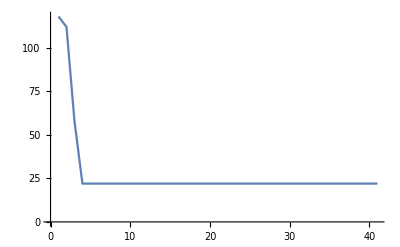
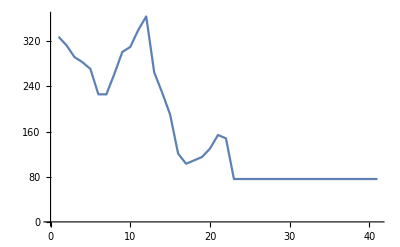
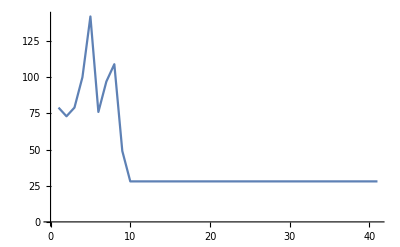
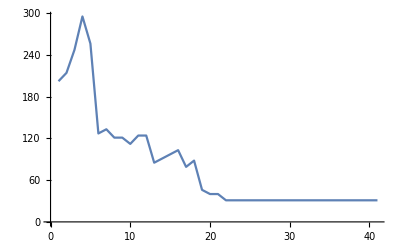
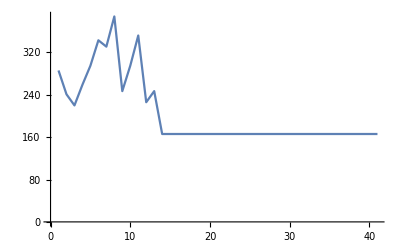
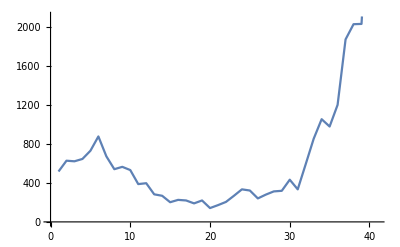
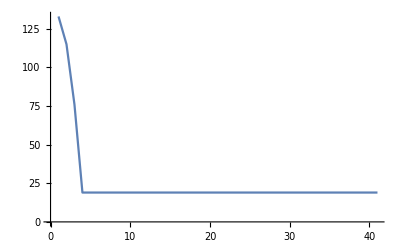
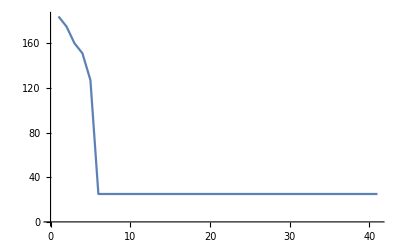
{{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False}}

```mathematica
Table[TestClassifierRasterize[RasterClassify,RasterTrain],50]
```

#### Thoughts

Perhaps it’s training on the last few lines of the raster. Try feature set identification:

```mathematica
ImportDataset["5to50_40_10000_rastertest.mx"]
```

```mathematica
rasternet = NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
rasterfeatureFunction=Take[rasternet,{1,"fc7"}]
```

NetChain[<>]

```mathematica
rastertraining = Keys[RasterTest];
```

```mathematica
RasterTest
```

{-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→15,-Graphics-→3,-Graphics-→6,-Graphics-→12,-Graphics-→3,-Graphics-→3,-Graphics-→8,-Graphics-→3,-Graphics-→11,-Graphics-→4,-Graphics-→9,-Graphics-→6,-Graphics-→17,-Graphics-→2,-Graphics-→8,-Graphics-→3,-Graphics-→9,-Graphics-→8,-Graphics-→4,-Graphics-→11,-Graphics-→5,-Graphics-→3,-Graphics-→5,-Graphics-→15,-Graphics-→5,-Graphics-→9,-Graphics-→5,-Graphics-→4,-Graphics-→3,-Graphics-→5,-Graphics-→3,-Graphics-→3,-Graphics-→12,-Graphics-→15,-Graphics-→6,-Graphics-→9,-Graphics-→8,-Graphics-→39,-Graphics-→9,-Graphics-→7,-Graphics-→8,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→7,-Graphics-→3,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→19,-Graphics-→2,-Graphics-→9,-Graphics-→20,-Graphics-→4,-Graphics-→3,-Graphics-→7,-Graphics-→6,-Graphics-→9,-Graphics-→5,-Graphics-→9,-Graphics-→13,-Graphics-→6,-Graphics-→7,-Graphics-→4,-Graphics-→7,-Graphics-→5,-Graphics-→3,-Graphics-→5,-Graphics-→12,-Graphics-→7,-Graphics-→8,-Graphics-→12,-Graphics-→3,-Graphics-→5,-Graphics-→10,-Graphics-→4,-Graphics-→11,-Graphics-→3,-Graphics-→10,-Graphics-→2,-Graphics-→19,-Graphics-→5,-Graphics-→8,-Graphics-→6,-Graphics-→11,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→7,-Graphics-→4,-Graphics-→7,-Graphics-→5,-Graphics-→14,-Graphics-→6,-Graphics-→7,-Graphics-→9,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→12,-Graphics-→5,-Graphics-→14,-Graphics-→3,-Graphics-→6,-Graphics-→9,-Graphics-→6,-Graphics-→5,-Graphics-→6,-Graphics-→11,-Graphics-→8,-Graphics-→10,-Graphics-→11,-Graphics-→6,-Graphics-→3,-Graphics-→6,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→20,-Graphics-→6,-Graphics-→5,-Graphics-→6,-Graphics-→8,-Graphics-→7,-Graphics-→3,-Graphics-→6,-Graphics-→6,-Graphics-→3,-Graphics-→6,-Graphics-→7,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→21,-Graphics-→8,-Graphics-→15,-Graphics-→4,-Graphics-→11,-Graphics-→3,-Graphics-→4,-Graphics-→5,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→9,-Graphics-→5,-Graphics-→9,-Graphics-→4,-Graphics-→3,-Graphics-→6,-Graphics-→9,-Graphics-→7,-Graphics-→8,-Graphics-→5,-Graphics-→12,-Graphics-→4,-Graphics-→4,-Graphics-→12,-Graphics-→9,-Graphics-→4,-Graphics-→9,-Graphics-→7,-Graphics-→3,-Graphics-→12,-Graphics-→4,-Graphics-→4,-Graphics-→9,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→10,-Graphics-→14,-Graphics-→8,-Graphics-→6,-Graphics-→14,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→20,-Graphics-→5,-Graphics-→13,-Graphics-→3,-Graphics-→7,-Graphics-→4,-Graphics-→6,-Graphics-→10,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→2,-Graphics-→8,-Graphics-→6,-Graphics-→5,-Graphics-→8,-Graphics-→4,-Graphics-→12,-Graphics-→9,-Graphics-→5,-Graphics-→7,-Graphics-→4,-Graphics-→6,-Graphics-→10,-Graphics-→22,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→7,-Graphics-→5,-Graphics-→2,-Graphics-→15,-Graphics-→6,-Graphics-→8,-Graphics-→5,-Graphics-→3,-Graphics-→8,-Graphics-→3,-Graphics-→7,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→5,-Graphics-→7,-Graphics-→8,-Graphics-→12,-Graphics-→6,-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→4,-Graphics-→9,-Graphics-→11,-Graphics-→3,-Graphics-→4,-Graphics-→22,-Graphics-→3,-Graphics-→4,-Graphics-→17,-Graphics-→13,-Graphics-→4,-Graphics-→6,-Graphics-→14,-Graphics-→7,-Graphics-→11,-Graphics-→4,-Graphics-→17,-Graphics-→3,-Graphics-→5,-Graphics-→13,-Graphics-→6,-Graphics-→4,-Graphics-→8,-Graphics-→7,-Graphics-→7,-Graphics-→5,-Graphics-→9,-Graphics-→6,-Graphics-→6,-Graphics-→2,-Graphics-→10,-Graphics-→4,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→9,-Graphics-→3,-Graphics-→8,-Graphics-→7,-Graphics-→28,-Graphics-→3,-Graphics-→5,-Graphics-→8,-Graphics-→8,-Graphics-→8,-Graphics-→3,-Graphics-→9,-Graphics-→4,-Graphics-→11,-Graphics-→8,-Graphics-→13,-Graphics-→6,-Graphics-→4,-Graphics-→9,-Graphics-→4,-Graphics-→3,-Graphics-→6,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→10,-Graphics-→17,-Graphics-→5,-Graphics-→15,-Graphics-→9,-Graphics-→10,-Graphics-→4,-Graphics-→7,-Graphics-→7,-Graphics-→15,-Graphics-→7,-Graphics-→12,-Graphics-→16,-Graphics-→5,-Graphics-→7,-Graphics-→3,-Graphics-→5,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→7,-Graphics-→8,-Graphics-→8,-Graphics-→4,-Graphics-→12,-Graphics-→3,-Graphics-→11,-Graphics-→17,-Graphics-→8,-Graphics-→12,-Graphics-→7,-Graphics-→20,-Graphics-→10,-Graphics-→7,-Graphics-→8,-Graphics-→8,-Graphics-→10,-Graphics-→12,-Graphics-→13,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→11,-Graphics-→16,-Graphics-→6,-Graphics-→11,-Graphics-→3,-Graphics-→5,-Graphics-→9,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→7,-Graphics-→17,-Graphics-→11,-Graphics-→6,-Graphics-→5,-Graphics-→4,-Graphics-→3,-Graphics-→7,-Graphics-→8,-Graphics-→4,-Graphics-→5,-Graphics-→7,-Graphics-→11,-Graphics-→14,-Graphics-→5,-Graphics-→3,-Graphics-→7,-Graphics-→3,-Graphics-→8,-Graphics-→8,-Graphics-→3,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→7,-Graphics-→6,-Graphics-→8,-Graphics-→12,-Graphics-→12,-Graphics-→5,-Graphics-→4,-Graphics-→6,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→11,-Graphics-→8,-Graphics-→11,-Graphics-→3,-Graphics-→5,-Graphics-→4,-Graphics-→6,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→5,-Graphics-→7,-Graphics-→4,-Graphics-→3,-Graphics-→9,-Graphics-→4,-Graphics-→7,-Graphics-→8,-Graphics-→4,-Graphics-→12,-Graphics-→6,-Graphics-→9,-Graphics-→10,-Graphics-→12,-Graphics-→19,-Graphics-→7,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→8,-Graphics-→4,-Graphics-→4,-Graphics-→13,-Graphics-→5,-Graphics-→7,-Graphics-→7,-Graphics-→12,-Graphics-→4,-Graphics-→13,-Graphics-→13,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→5,-Graphics-→12,-Graphics-→6,-Graphics-→5,-Graphics-→6,-Graphics-→8,-Graphics-→8,-Graphics-→14,-Graphics-→12,-Graphics-→17,-Graphics-→5,-Graphics-→16,-Graphics-→7,-Graphics-→8,-Graphics-→13,-Graphics-→9,-Graphics-→3,-Graphics-→12,-Graphics-→8,-Graphics-→10,-Graphics-→8,-Graphics-→4,-Graphics-→12,-Graphics-→9,-Graphics-→14,-Graphics-→8,-Graphics-→23,-Graphics-→4,-Graphics-→6,-Graphics-→4,-Graphics-→7,-Graphics-→11,-Graphics-→9,-Graphics-→8,-Graphics-→7,-Graphics-→7,-Graphics-→6,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→10,-Graphics-→14,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→6,-Graphics-→6,-Graphics-→14,-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→7,-Graphics-→3,-Graphics-→5,-Graphics-→6,-Graphics-→5,-Graphics-→4,-Graphics-→13,-Graphics-→7,-Graphics-→6,-Graphics-→2,-Graphics-→5,-Graphics-→9,-Graphics-→14,-Graphics-→2,-Graphics-→7,-Graphics-→3,-Graphics-→10,-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→7,-Graphics-→5,-Graphics-→7,-Graphics-→4,-Graphics-→3,-Graphics-→9,-Graphics-→4,-Graphics-→5,-Graphics-→11,-Graphics-→5,-Graphics-→3,-Graphics-→12,-Graphics-→38,-Graphics-→5,-Graphics-→15,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→7,-Graphics-→12,-Graphics-→5,-Graphics-→7,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→20,-Graphics-→3,-Graphics-→3,-Graphics-→5,-Graphics-→11,-Graphics-→4,-Graphics-→9,-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→6,-Graphics-→10,-Graphics-→13,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→14,-Graphics-→5,-Graphics-→3,-Graphics-→5,-Graphics-→10,-Graphics-→5,-Graphics-→3,-Graphics-→4,-Graphics-→28,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→12,-Graphics-→9,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→11,-Graphics-→8,-Graphics-→5,-Graphics-→4,-Graphics-→21,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→11,-Graphics-→4,-Graphics-→5,-Graphics-→3,-Graphics-→3,-Graphics-→9,-Graphics-→6,-Graphics-→8,-Graphics-→6,-Graphics-→11,-Graphics-→7,-Graphics-→14,-Graphics-→8,-Graphics-→6,-Graphics-→8,-Graphics-→8,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→5,-Graphics-→6,-Graphics-→5,-Graphics-→20,-Graphics-→3,-Graphics-→18,-Graphics-→10,-Graphics-→11,-Graphics-→3,-Graphics-→3,-Graphics-→7,-Graphics-→7,-Graphics-→9,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→9,-Graphics-→10,-Graphics-→12,-Graphics-→13,-Graphics-→5,-Graphics-→5,-Graphics-→4,-Graphics-→9,-Graphics-→16,-Graphics-→6,-Graphics-→7,-Graphics-→4,-Graphics-→9,-Graphics-→6,-Graphics-→8,-Graphics-→2,-Graphics-→10,-Graphics-→8,-Graphics-→9,-Graphics-→3,-Graphics-→13,-Graphics-→6,-Graphics-→3,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→10,-Graphics-→14,-Graphics-→6,-Graphics-→3,-Graphics-→7,-Graphics-→10,-Graphics-→3,-Graphics-→4,-Graphics-→22,-Graphics-→17,-Graphics-→5,-Graphics-→8,-Graphics-→11,-Graphics-→5,-Graphics-→36,-Graphics-→5,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→12,-Graphics-→5,-Graphics-→5,-Graphics-→3,-Graphics-→5,-Graphics-→3,-Graphics-→15,-Graphics-→3,-Graphics-→8,-Graphics-→3,-Graphics-→3,-Graphics-→6,-Graphics-→12,-Graphics-→11,-Graphics-→2,-Graphics-→12,-Graphics-→6,-Graphics-→4,-Graphics-→14,-Graphics-→3,-Graphics-→3,-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→7,-Graphics-→2,-Graphics-→3,-Graphics-→5,-Graphics-→4,-Graphics-→12,-Graphics-→12,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→11,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→3,-Graphics-→6,-Graphics-→3,-Graphics-→6,-Graphics-→10,-Graphics-→8,-Graphics-→16,-Graphics-→8,-Graphics-→10,-Graphics-→6,-Graphics-→6,-Graphics-→8,-Graphics-→7,-Graphics-→19,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→False}

```mathematica
rasterfeatures=Monitor[Table[rasterfeatureFunction[rastertraining[[x]]],{x,1,Length[rastertraining]}],x];
```

```mathematica
xyz = DimensionReduce[features,3,Method->"TSNE"];
Graphics3D[
MapThread[Inset[Thumbnail[RemoveBackground@#2,32],#1]&,{xyz,rastertraining}],
BoxRatios->{1, 1, 1}
]
```

DimensionReduce::mlmpty: The dataset should contain at least one example.

MapThread::mptd: Object DimensionReduce[features,3,Method→TSNE] at position {2, 1} in MapThread[Inset[Thumbnail[RemoveBackground[#2],32],#1]&,{DimensionReduce[features,3,Method→TSNE],rastertraining}] has only 0 of required 1 dimensions.

-Graphics3D-

```mathematica
cl=Classify[RasterTest,FeatureExtractor->rasterfeatureFunction]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[cl]
```

Classifier information
Input type | Image
Number of classes | 27
Method | NearestNeighbors
Accuracy | 64.8 % ± 4. %
Loss | 1.44 ± 0.18
Single evaluation time | 1.01 s/example
Batch evaluation speed | 1.83 examples/s
Classifier memory | 585. MB
Training examples used | 1456 examples
Training time | 15 28
 |

```mathematica
cl[
```